Delta potential at x = aa of strength uu, hard wall at x < 0.

```mathematica
psi1[x_] := AA Sin[k x]
psi2[x_] := Exp[-I k x] + RR Exp[I k x]
```

```mathematica
psi[x_] := If[x < aa,psi1[x],psi2[x]]
```

```mathematica
Solve[{
psi1[aa] == psi2[aa],
psi2'[aa] - psi1'[aa] == uu psi1[aa]},
{AA, RR}]
```

{{AA→(2 ⅇ^(-ⅈ aa k) k)/(ⅈ k Cos[aa k]+k Sin[aa k]+ⅈ uu Sin[aa k]),RR→-ⅇ^(-2 ⅈ aa k)+(2 ⅇ^(-2 ⅈ aa k) k Sin[aa k])/(ⅈ k Cos[aa k]+k Sin[aa k]+ⅈ uu Sin[aa k])}}

```mathematica
RR := -ⅇ^(-2 ⅈ aa k)+(2 ⅇ^(-2 ⅈ aa k) k Sin[aa k])/(ⅈ k Cos[aa k]+k Sin[aa k]+ⅈ uu Sin[aa k])
AA:=(2 ⅇ^(-ⅈ aa k) k)/(ⅈ k Cos[aa k]+k Sin[aa k]+ⅈ uu Sin[aa k])
```

```mathematica
aa := 1
uu := 20
```

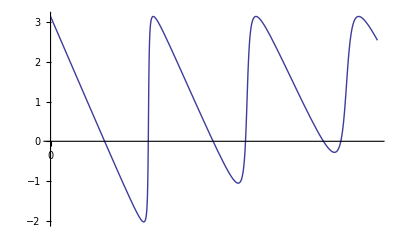

```mathematica
Plot[Arg[RR], {k, 0.0, 10.0}, Ticks->{Range[0, 100 * Pi, Pi], Automatic}]
```

```mathematica
Plot3D[Norm[psi[x]],{x,0.0,3.0},{k,0.0, 3 * Pi}, ImageSize-> Full]
```

-Graphics3D-

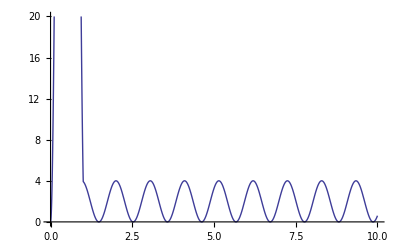

```mathematica
Plot[Norm[psi[x] /. {k -> 2.99591}]^2, {x, 0.0, 10.0}, PlotRange->{Automatic, {0.0, 20.0}}]
```

```mathematica
FindMaximum[FindMaxValue[Norm[psi[x]]^2, {x, 0.5}],{k,6.28}]
```

FindMaxValue::nrnum: The function value -Norm[2\ ⅇ^-ⅈ\ k\ k\ Sin[0.5\ k]/ⅈ\ k\ Cos[« 1 »] + 20\ ⅈ\ Sin[« 1 »] + k\ Sin[« 1 »]]^2 is not a real number at {x} = {0.5}.

General::stop: Further output of FindMaxValue :: nrnum will be suppressed during this calculation.

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue :: lstol will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{51.9575,{k→6.01173}}